```mathematica
c := 3*10^(10) 
G:= 6.67*10^(-8)
hbar := 1.054*10^(-27) (* cte de plack reducida*)
kb := 1.3806*10^(-16) (* cte de boltzmann*)
```

```mathematica
gstar := 10.75 (* grados de libertad*)
TBBN := (10^6*1.6*10^(-12))/kb  (* temperatura en BBN [K]*)
```

```mathematica
ρradBBN = π^2/30*gstar*(kb^4*TBBN^4)/(hbar*c)^3
```

7.33131×10^26

```mathematica
β := 10^(-8)
ρ0 =β*ρradBBN
```

7.33131×10^18

```mathematica
ati := 1.66*10^(-10)
ti := 0.74 (*s*)
```

```mathematica
n:=1
k = (4π *G)/(3*c^2)*ρ0 *(ati)^(3-n)
```

6.27147×10^-29

```mathematica
Hti = √((8π G)/(3c^2)(ρradBBN + ρ0))
```

0.67467

```mathematica
Dati := Hti * ati (* 1/s*)
```

```mathematica
A := 2ati^2*Hti -2k ti
B := ati^2 +k *ti-2ati^2*Hti*ti
```

```mathematica
A
B
```

3.71824×10^-20

4.1001×10^-23

```mathematica
a1[t_]:= √(k t^2+A t+B)
```

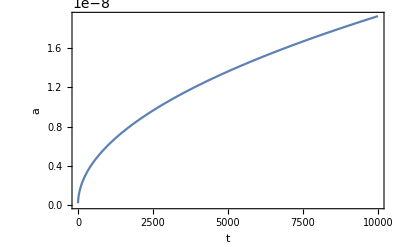

```mathematica
Plot[a1[t], {t, ti, 10000}, AxesLabel->{t,a},Frame->True, PlotRangePadding->0 ]
```

```mathematica
ar := ati/ti^(1/2)
aRad[t_]:= ar*t^(1/2)
```

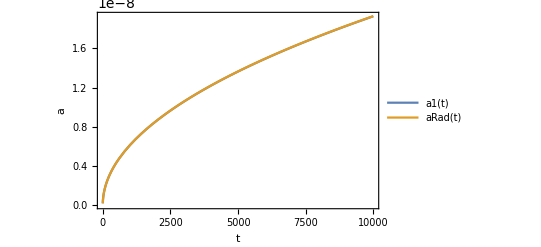

```mathematica
Plot[{a1[t], aRad[t]}, {t, ti, 10000}, PlotLegends->"Expressions", AxesLabel->{t,a}, Frame->True, PlotRangePadding->0]
```

```mathematica
D[a1[t], t]
```

(A+2 k t)/(2 √(B+A t+k t^2))

```mathematica
Da[t_]:=(A+2 k t)/(2 √(B+A t+k t^2))
```

```mathematica
ρcf[t_]= (3c^2)/(8π G)(Da[t]/a1[t])^2-ρ0 (ati/a1[t])^(3-n)
```

(3 c^2 (A+2 k t)^2)/(32 G π (B+A t+k t^2)^2)-(ati/(√(B+A t+k t^2)))^(3-n) ρ0

```mathematica
Temp100MeV:= (100*10^6*1.6*10^(-12))/kb
ρradBBNTemp100Mev = π^2/30*gstar*(kb^4*Temp100MeV^4)/(hbar*c)^3
```

7.33131×10^34

```mathematica
ρcf[10^(-4)]
```

2.78372×10^32

```mathematica
Temp10m4 = ((30*(hbar*c)^3*ρcf[10^(-4)])/(π^2*gstar*kb^4))^(1/4)*kb/(1.6*10^(-12))
```

2.48234×10^7

```mathematica
Temp[t_] := ((30*(hbar*c)^3*ρcf[t])/(π^2*gstar*kb^4))^(1/4)*kb/(1.6*10^(-12))
```

```mathematica
Temp[10^(-25)]
```

2.59245×10^7

```mathematica
ρcf[10^(-30)]
```

3.31151×10^32

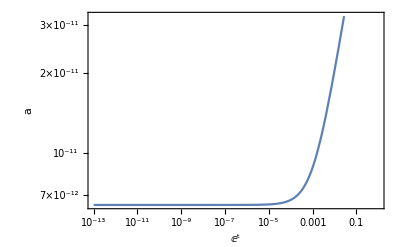

```mathematica
LogLogPlot[a1[t], {t,10^(-13),1}, AxesLabel->{t,a},Frame->True, PlotRangePadding->0 ]
```